# Error Averaging Paper Graphs

```mathematica
Colours
```

```mathematica
blue=RGBColor[55/255,126/255,184/255];
red=RGBColor[228/255,26/255,28/255];
green=RGBColor[77/255,175/255,74/255];
```

## Fig 1

```mathematica
aDaggera[n_,v_]:=1-((2*n-1)*v)/(4*n);
aDaggeraWps[n_,v_]:=1-v/(4*n);
bDaggerb[n_,v_]:=v/(4*n);
```

```mathematica
bDaggerbWps[n_,v_]:=v/(4*n)/Psuccess[n,v];
```

```mathematica
Psuccess[n_,v_]:=1+v/(2*n)-v/2;
```

```mathematica
v=0.5;

ClearAll[hatchF]
hatchF[mf_List: {#&,#2&},mesh_List: {50,50},style_: GrayLevel[.5],opts:OptionsPattern[]]:=ParametricPlot[{x,y},{x,0,1},{y,0,1},Mesh->mesh,MeshFunctions->mf,MeshStyle->style,BoundaryStyle->None,opts,Frame->False,PlotRangePadding->0,ImagePadding->0,Axes->False]
t1=hatchF[{#-#2&},{100},White,MeshShading->{green,green}];
t2=hatchF[{#-#2&},{40},White,MeshShading->{red,red}];

BarChart[{{aDaggera[1,v],bDaggerb[1,v],1-Psuccess[1,v]},{aDaggera[8,v],bDaggerb[8,v],1-Psuccess[8,v]},{aDaggera[8,v]/Psuccess[8,v],bDaggerb[8,v]/Psuccess[8,v],0}},BaseStyle->{FontSize->16},ChartLabels->{{"N=1 (No Correction)","N=8 Without Postselection","N=8 With Postselection"},None},Frame->{True,True,False,False},FrameLabel->{,"Probability"},ChartStyle->{blue,Texture[t1],Texture[t2]},ChartElementFunction->System`BarFunctionDump`TextureBar (*ChartStyle->{"Gold"}*)]
```

-Graphics-

```mathematica
EdgeForm/@{Thin,Dashed,Dotted}
```

{EdgeForm[Thickness[Tiny]],EdgeForm[Dashing[{Small,Small}]],EdgeForm[Dashing[{0,Small}]]}

```mathematica
ChartStyle->{RGBColor[252,141,89],RGBColor[255,255,191],RGBColor[145,207,96]}
```

ChartStyle→{RGBColor[252,141,89],RGBColor[255,255,191],RGBColor[145,207,96]}

## Fig 4

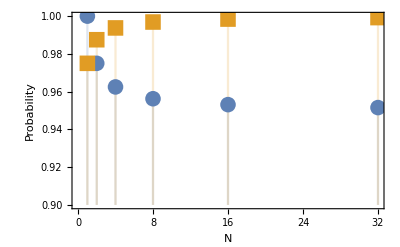

```mathematica
DiscretePlot[{1+0.1/(2*n)-0.1/2,1-0.1/(4n)},{n,{1,2,4,8,16,32}},PlotRange->{0.9,1},PlotMarkers->{Automatic,16},Frame->{True,True,False,False},FrameLabel->{"N","Probability"},BaseStyle->{FontSize->14}]
```

## Fig 6

```mathematica
v=.;
m=.;
n=.;
noAve[m_,n_,v_]:=1-(m*v)/4+(m^2 v^2)/16;
AveEnd[m_,n_,v_]:=(1-1/4(m*v-(m^2*v^2)/4+(1-1/n)*(m*v-1/2 m^2*v^2)))*(1-(1-1/n)*((m*v)/2-1/4 m^2*v^2))^-1;
AveStep[m_,n_,v_]:=(3/4-(m*v)/4+(m^2*v^2)/16+1/4(1-(v-v^2/2)*(1-1/n))^m)*(1/2+1/2(1-(v-v^2/2)(1-1/n))^m)^-1;
errnoav[m_,n_,v_]:=1-0.25m*v+0.0625*m^2*v^2
erravend[m_,n_,v_]:=(1-0.25m*v+0.0625*m^2*v^2-(0.25m*v-0.125*m^2*v^2)*(1-1/n))*(1-(0.5*m*v-0.25*m^2*v^2)*(1-1/n))^(-1)
erravstep[m_,n_,v_]:=(0.75-0.25m*v+0.0625*m^2*v^2+0.25*(1-(v-0.5*v^2)*(1-1/n))^m)*((0.5+0.5*(1-(v-0.5*v^2)*(1-1/n))^m))^(-1)
```

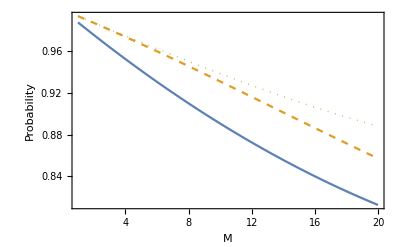

```mathematica
v=0.05;
n=2;
Plot[{noAve[m,n,v],AveEnd[m,n,v],AveStep[m,n,v]},{m,1,20},Frame->{True,True,False,False},FrameLabel->{"M","Probability"},AxesOrigin->{1,Automatic},PlotStyle->{,Directive[Dashed],Directive[Dotted,Thick]},BaseStyle->{FontSize->14}]
```

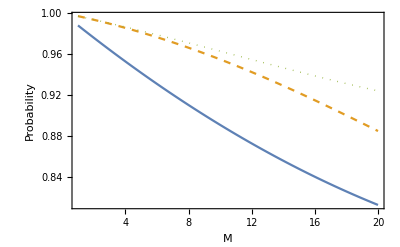

```mathematica
n=4;
Plot[{noAve[m,n,v],AveEnd[m,n,v],AveStep[m,n,v]},{m,1,20},(*AxesOrigin->{0,Automatic},*)Frame->{True,True,False,False},FrameLabel->{"M","Probability"},AxesOrigin->{1,Automatic},PlotStyle->{,Directive[Dashed],Directive[Dotted,Thick]},BaseStyle->{FontSize->14}]
```

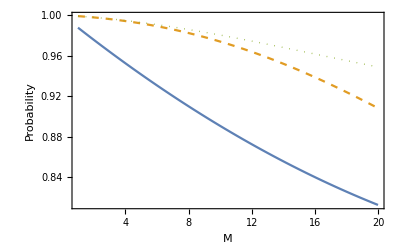

```mathematica
n=16;
Plot[{noAve[m,n,v],AveEnd[m,n,v],AveStep[m,n,v]},{m,1,20},(*AxesOrigin->{0,Automatic},*)Frame->{True,True,False,False},FrameLabel->{"M","Probability"},AxesOrigin->{1,Automatic},PlotStyle->{,Directive[Dashed],Directive[Dotted,Thick]},BaseStyle->{FontSize->14}]
```

## Fig 7 (probably)

```mathematica
(*Exact Cos term (inlcuding sum) when averaging at the end*)
cend[m_,n_,v_]:=(j=0;Do[j=(Cos[m*Mean[RandomVariate[NormalDistribution[ave,Sqrt[v]],m]]-m*Mean[RandomVariate[NormalDistribution[ave,Sqrt[v]],m]]])+j,{i,1,(0.5*n^2-0.5*n)}];j)
```

RandomVariate::realprm: Parameter ave at position 1 in NormalDistribution[ave,0.0707107] is expected to be real.

General::stop: Further output of RandomVariate::realprm will be suppressed during this calculation.

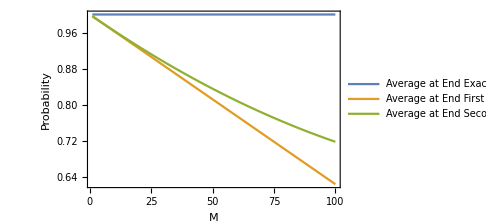

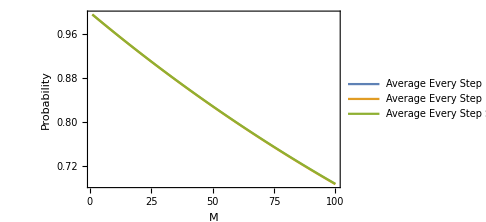

```mathematica
v=0.005;
n=4;
mmax=100;
DiscretePlot[{1/(n^2)*(n+2*cend[m,n,v]),1-v*m*(1-1/n),1-(v*m-0.5*m^2*v^2)*(1-1/n)},{m,mmax},PlotLegends->{"Average at End Exact Value","Average at End First Order Approximation","Average at End Second Order Approximation"}(*,PlotLabel->{"Probability of Success with v = ", v, "N = ",n}*),AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium]
DiscretePlot[{1/(n^(2*m))*(step[m,n,v]),(1-v*(1-1/n))^m,(1-(v-0.5*v^2)*(1-1/n))^m},{m,mmax},PlotLegends->{"Average Every Step Exact Value","Average Every Step First Order Approximation","Average Every Step Second Order Approximation"},(*PlotLabel->{"Probability of Success with v = ", v, "N = ",n},*)AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium]
```

RandomVariate::realprm: Parameter ave at position 1 in NormalDistribution[ave,0.0707107] is expected to be real.

General::stop: Further output of RandomVariate::realprm will be suppressed during this calculation.

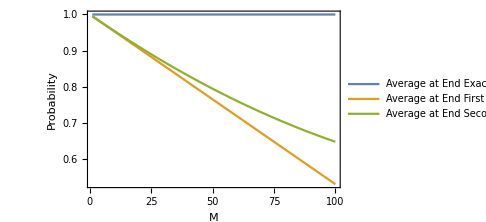

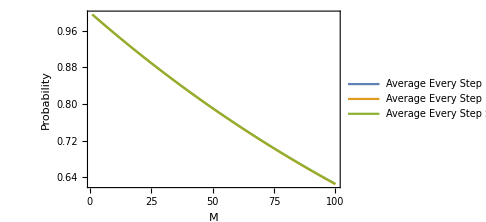

```mathematica
v=0.005;
n=16;
mmax=100;
DiscretePlot[{1/(n^2)*(n+2*cend[m,n,v]),1-v*m*(1-1/n),1-(v*m-0.5*m^2*v^2)*(1-1/n)},{m,mmax},PlotLegends->{"Average at End Exact Value","Average at End First Order Approximation","Average at End Second Order Approximation"}(*,PlotLabel->{"Probability of Success with v = ", v, "N = ",n}*),AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium]
DiscretePlot[{1/(n^(2*m))*(step[m,n,v]),(1-v*(1-1/n))^m,(1-(v-0.5*v^2)*(1-1/n))^m},{m,mmax},PlotLegends->{"Average Every Step Exact Value","Average Every Step First Order Approximation","Average Every Step Second Order Approximation"},(*PlotLabel->{"Probability of Success with v = ", v, "N = ",n},*)AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium]
```

RandomVariate::realprm: Parameter ave at position 1 in NormalDistribution[ave,0.316228] is expected to be real.

General::stop: Further output of RandomVariate::realprm will be suppressed during this calculation.

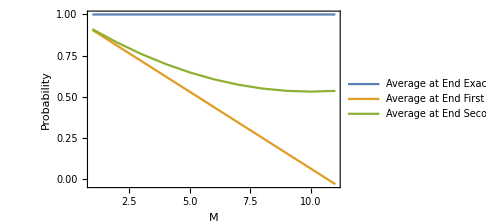

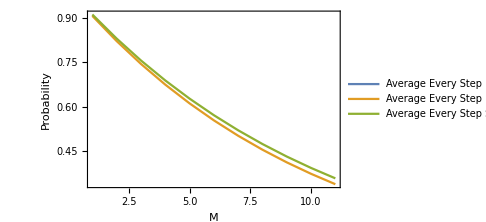

```mathematica
v=0.1;
n=16;
mmax=11;
DiscretePlot[{1/(n^2)*(n+2*cend[m,n,v]),1-v*m*(1-1/n),1-(v*m-0.5*m^2*v^2)*(1-1/n)},{m,mmax},PlotLegends->{"Average at End Exact Value","Average at End First Order Approximation","Average at End Second Order Approximation"}(*,PlotLabel->{"Probability of Success with v = ", v, "N = ",n}*),AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium]
DiscretePlot[{1/(n^(2*m))*(step[m,n,v]),(1-v*(1-1/n))^m,(1-(v-0.5*v^2)*(1-1/n))^m},{m,mmax},PlotLegends->{"Average Every Step Exact Value","Average Every Step First Order Approximation","Average Every Step Second Order Approximation"},(*PlotLabel->{"Probability of Success with v = ", v, "N = ",n},*)AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium]
```

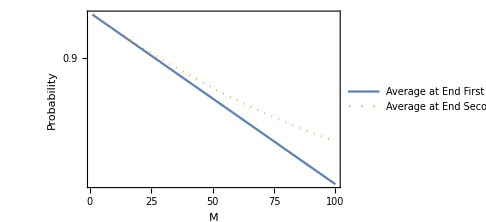

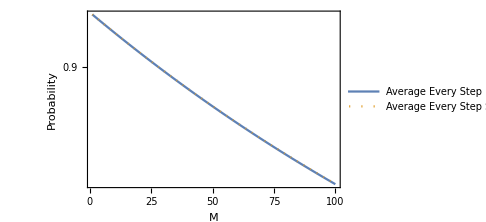

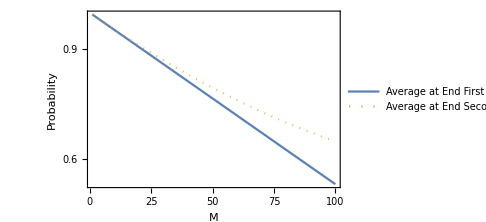

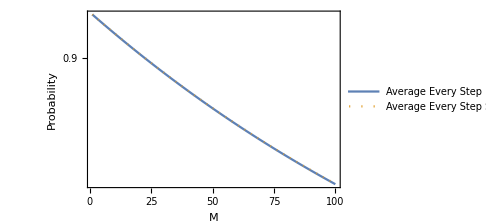

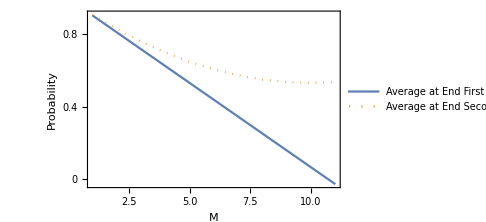

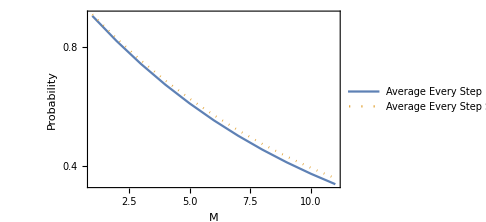

```mathematica
v=0.005;
n=4;
mmax=100;
DiscretePlot[{1-v*m*(1-1/n),1-(v*m-0.5*m^2*v^2)*(1-1/n)},{m,mmax},PlotLegends->{"Average at End First Order Approximation","Average at End Second Order Approximation"}(*,PlotLabel->{"Probability of Success with v = ", v, "N = ",n}*),AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium,AxesOrigin->{1,Automatic},PlotStyle->{,Directive[Dotted,Thick]},BaseStyle->{FontSize->19},FrameTicks->{{Automatic},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}}]
DiscretePlot[{(1-v*(1-1/n))^m,(1-(v-0.5*v^2)*(1-1/n))^m},{m,mmax},PlotLegends->{"Average Every Step First Order Approximation","Average Every Step Second Order Approximation"},(*PlotLabel->{"Probability of Success with v = ", v, "N = ",n},*)AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium,PlotStyle->{,Directive[Dotted,Thick]},BaseStyle->{FontSize->18},FrameTicks->{{Automatic},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}}]

v=0.005;
n=16;
mmax=100;
DiscretePlot[{1-v*m*(1-1/n),1-(v*m-0.5*m^2*v^2)*(1-1/n)},{m,mmax},PlotLegends->{"Average at End First Order Approximation","Average at End Second Order Approximation"}(*,PlotLabel->{"Probability of Success with v = ", v, "N = ",n}*),AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium,PlotStyle->{,Directive[Dotted,Thick]},BaseStyle->{FontSize->18},FrameTicks->{{Automatic},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}}]
DiscretePlot[{(1-v*(1-1/n))^m,(1-(v-0.5*v^2)*(1-1/n))^m},{m,mmax},PlotLegends->{"Average Every Step First Order Approximation","Average Every Step Second Order Approximation"},(*PlotLabel->{"Probability of Success with v = ", v, "N = ",n},*)AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium,PlotStyle->{,Directive[Dotted,Thick]},BaseStyle->{FontSize->18},FrameTicks->{{Automatic},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}}]

v=0.1;
n=16;
mmax=11;
DiscretePlot[{1-v*m*(1-1/n),1-(v*m-0.5*m^2*v^2)*(1-1/n)},{m,mmax},PlotLegends->{"Average at End First Order Approximation","Average at End Second Order Approximation"}(*,PlotLabel->{"Probability of Success with v = ", v, "N = ",n}*),AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium,PlotStyle->{,Directive[Dotted,Thick]},BaseStyle->{FontSize->18},FrameTicks->{{Automatic},{0,0.2,0.4,0.6,0.8,1.0}}]
DiscretePlot[{(1-v*(1-1/n))^m,(1-(v-0.5*v^2)*(1-1/n))^m},{m,mmax},PlotLegends->{"Average Every Step First Order Approximation","Average Every Step Second Order Approximation"},(*PlotLabel->{"Probability of Success with v = ", v, "N = ",n},*)AxesLabel->{"M",},Joined->True,Filling->False,Frame->{True,True,False,False},FrameLabel->{"M","Probability"},ImageSize->Medium,PlotStyle->{,Directive[Dotted,Thick]},BaseStyle->{FontSize->18},FrameTicks->{{Automatic},{0,0.2,0.4,0.6,0.8,1.0}}]
```

## Fig 8 (prob)

```mathematica
ave=0;
v=.;
n=.;
m=.;

θnoav[v_,m_]:=Re[FullSimplify[-I*Log[Exp[I*m*Mean[RandomVariate[NormalDistribution[ave,Sqrt[v]],m]]]]]]

θavstep[v_,n_,m_]:=Re[FullSimplify[-I*Log[stateavstep[v,n,m]]]]
stateavstep[v_,n_,m_]:=(a=1/(n^m);Do[{e=0,Do[e=e+Exp[I*RandomVariate[NormalDistribution[ave,Sqrt[v]],1][[1]]],{j,1,n}],a=a*e},{k,1,m}];FullSimplify[ComplexExpand[a/Sqrt[a*Conjugate[a]]]])

θavend[v_,n_,m_]:=Re[FullSimplify[-I*Log[stateavend[v,n,m]]]]
stateavend[v_,n_,m_]:=(e=0;Do[{a=Exp[I*m*Mean[RandomVariate[NormalDistribution[ave,Sqrt[v]],m]]],e=e+a},{j,1,n}];e=e/n;FullSimplify[ComplexExpand[e/Sqrt[e*Conjugate[e]]]])
```

```mathematica
runs=5000;
thetaNoAv=Range[runs];
thetaAvEnd=Range[runs];
thetaAvStep=Range[runs];

v=0.3;
n=4;
m=8;

Do[{thetaNoAv[[i]]=θnoav[v,m],thetaAvEnd[[i]]=θavend[v,n,m],thetaAvStep[[i]]=θavstep[v,n,m]},{i,1,runs}]

varNoAv=Variance[thetaNoAv];
varAvEnd=Variance[thetaAvEnd];
varAvStep=Variance[thetaAvStep];

Print["The variance of each phase shifter is ", v];
Print["M times the variance of each phase shifter is ", m*v];
Print["The variance of θ_total without averaging is ", varNoAv];
Print["M/N times the variance of each phase shifter is ", m*v/n];
Print["The variance of θ_total with averaging at the end is ", varAvEnd];
Print["The variance of θ_total with averaging at each step is ", varAvStep];
Print["This is all based on ", runs" runs"]
```

The variance of each phase shifter is 0.3

M times the variance of each phase shifter is 2.4

The variance of θ_total without averaging is 2.10674

M/N times the variance of each phase shifter is 0.6

The variance of θ_total with averaging at the end is 1.33703

The variance of θ_total with averaging at each step is 0.604185

This is all based on 5000  runs

```mathematica
ClearAll[hatchF]
hatchF[mf_List: {#&,#2&},mesh_List: {50,50},style_: GrayLevel[.5],opts:OptionsPattern[]]:=ParametricPlot[{x,y},{x,0,1},{y,0,1},Mesh->mesh,MeshFunctions->mf,MeshStyle->style,BoundaryStyle->None,opts,Frame->False,PlotRangePadding->0,ImagePadding->0,Axes->False]
t1=hatchF[{#-#2&},{60},White,MeshShading->{green,green}];
t2=hatchF[{#-#2&,#2+#&},{40},Gray,PlotStyle->None,MeshShading->{{red,red},{red,red}}];
```

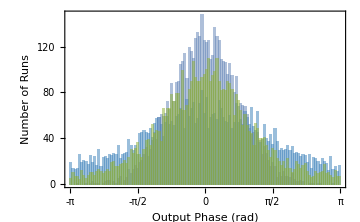

```mathematica
Histogram[{thetaNoAv,thetaAvStep,thetaAvEnd},100,ChartLegends->{"No Averaging","Averaging at Each Step","Averaging at End"},ImageSize->Medium,PlotRange->{{-Pi,Pi},Automatic},AxesOrigin->{-Pi,0},Frame->{True,True,False,False},FrameLabel->{"Output Phase (rad)","Number of Runs"},FrameTicks->{{Automatic,None},{{-Pi,-Pi/2,0,Pi/2,Pi},None}},BaseStyle->{FontSize->14},ChartStyle->{blue,Texture[t1],Texture[t2]},ChartElementFunction->System`BarFunctionDump`TextureBar]
```

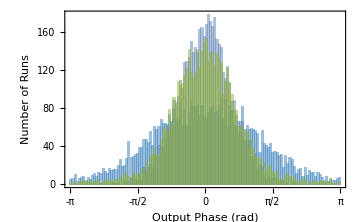

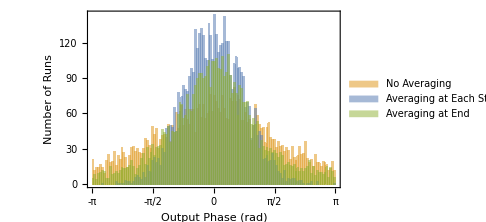

```mathematica
o=0.55;
Histogram[{thetaNoAv,thetaAvStep,thetaAvEnd},100,ChartLegends->{"No Averaging","Averaging at Each Step","Averaging at End"},ImageSize->Medium,PlotRange->{{-Pi,Pi},Automatic},AxesOrigin->{-Pi,0},Frame->{True,True,False,False},FrameLabel->{"Output Phase (rad)","Number of Runs"},ChartStyle->{RGBColor[0.880722,0.611041,0.142051,o],RGBColor[0.368417,0.506779,0.709798,o],Opacity[0.5,RGBColor[0.560181,0.691569,0.194885,o]]},FrameTicks->{{Automatic,None},{{-Pi,-Pi/2,0,Pi/2,Pi},None}},BaseStyle->{FontSize->14}]
```

```mathematica
FrameTicks->{{-Pi,-Pi/2,0,Pi/2,Pi},None},
```

```mathematica
runs=5000;
thetaNoAv=Range[runs];
thetaAvEnd=Range[runs];
thetaAvStep=Range[runs];

v=0.3;
n=4;
m=8;

Do[{thetaNoAv[[i]]=θnoav[v,m],thetaAvEnd[[i]]=θavend[v,n,m],thetaAvStep[[i]]=θavstep[v,n,m]},{i,1,runs}]

varNoAv=Variance[thetaNoAv];
varAvEnd=Variance[thetaAvEnd];
varAvStep=Variance[thetaAvStep];

Print["The variance of each phase shifter is ", v];
Print["M times the variance of each phase shifter is ", m*v];
Print["The variance of θ_total without averaging is ", varNoAv];
Print["M/N times the variance of each phase shifter is ", m*v/n];
Print["The variance of θ_total with averaging at the end is ", varAvEnd];
Print["The variance of θ_total with averaging at each step is ", varAvStep];
Print["This is all based on ", runs" runs"]
```

The variance of each phase shifter is 0.3

M times the variance of each phase shifter is 2.4

The variance of θ_total without averaging is 2.06194

M/N times the variance of each phase shifter is 0.6

The variance of θ_total with averaging at the end is 1.3554

The variance of θ_total with averaging at each step is 0.599795

This is all based on 5000  runs

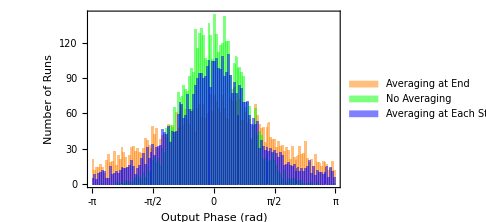

```mathematica
Histogram[{thetaNoAv,thetaAvStep,thetaAvEnd},100,FrameTicks->{{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},ChartLegends->{"Averaging at End","No Averaging","Averaging at Each Step"},ImageSize->Medium,PlotRange->{{-Pi,Pi},Automatic},AxesOrigin->{-Pi,0},Frame->{True,True,False,False},FrameLabel->{"Output Phase (rad)","Number of Runs"},ChartStyle->{Orange,Green,Blue}]
```

## Fig 9

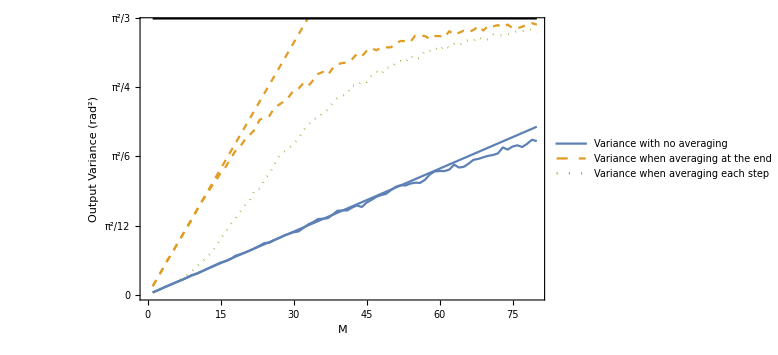

```mathematica
noAveVar1={0.09990302787648074,0.1999271076011517,0.2989710932065836,0.41117088278668334,0.491720377769649,0.5976997133797425,0.694499369027701,0.7921663434523104,0.8883249388081048,0.9953776713298302,1.1003305025193604,1.1798065132509836,1.2796179033118245,1.355072934440057,1.4515771619967144,1.520655165512725,1.6140344261974593,1.711166798261946,1.7637510233689442,1.8485702510369344,1.9038270720094397,1.9663375516660275,2.083333525227472,2.103381728272704,2.128368503232498,2.220807376671124,2.263124444165495,2.3009271249204115,2.3553884461484826,2.4338407402923425,2.4541270413175607,2.5194127943318954,2.4865524696171555,2.5525284254381058,2.628237493241088,2.652113969505083,2.6148899835453974,2.694118645354107,2.7444502598486364,2.758394771438141,2.764996754484519,2.803102402141907,2.8674698496795443,2.8391155152054814,2.902842754993092,2.935881220756511,2.910535728242162,2.944456038378318,2.944853480219304,2.9457743804500085,2.992043494700841,3.0214889755400103,3.017997030031496,3.0087383268944707,3.0865552784293846,3.0862316520495705,3.0803718561388838,3.0432326256011253,3.0792108342421547,3.079249574619388,3.063943733601517,3.138509490640972,3.096196745898661,3.1190924138261105,3.144791029659163,3.12769364797608,3.1534807173694426,3.198413469332609,3.1457211254416086,3.2017792753453427,3.1962185781685832,3.2099579069733535,3.184989591786008,3.217208945543949,3.17514852655353,3.1739249807514613,3.1904682529633535,3.219263734049718,3.2333696113618258,3.215632274241882};
aveEndVar1={0.024375481566751952,0.05105846672059418,0.07515681698088364,0.10246662099874097,0.12731619360486193,0.15711902011260265,0.18937840017220273,0.23109054170118037,0.2711183591003922,0.33577828669559756,0.37653626654338657,0.44413278921991556,0.49277237154544334,0.5721004010793018,0.6687422610155694,0.7441191620796571,0.8351821402796082,0.9041894925167554,0.9853438178893806,1.061633859477569,1.123528234041785,1.2493052770822668,1.2609390553228135,1.3763661085549996,1.4376849670509668,1.5476714749663998,1.6485635389828108,1.7014689421258617,1.7430053161754209,1.7931824551629265,1.8613525129967334,1.9571509777651175,2.019446767509704,2.094789033115106,2.099031295286159,2.1696961444351532,2.201170889341962,2.2848983456755483,2.342868458944071,2.367063625833732,2.3890799808382317,2.492822940139,2.4811159860983234,2.5428571468514014,2.5331915283441324,2.6070927311758307,2.6594003563158153,2.6239662569444135,2.7047169057009737,2.7012051057053745,2.7634324740335385,2.782718604260734,2.76578434097643,2.8457830880189205,2.801279265811594,2.822457836102652,2.905922227270893,2.9079182618101007,2.9433095789334565,2.9034284537289756,2.969726481549842,2.937957011614095,2.9824831027748377,2.962545224660601,3.0188081808769076,3.0306722721472874,3.024201599603128,3.0700539600526464,3.02733654781281,3.0426832408673183,3.0942926702490112,3.0940650687019207,3.0880629810928157,3.0990510586285995,3.120699822657449,3.1408111022388594,3.1375850975853425,3.1462001062727865,3.1615258120582004,3.1186960478851535};
aveStepVar1={0.025037237351799458,0.04885938387520467,0.07656486797548154,0.1024761246416241,0.1249480508946686,0.1517706681655276,0.17261661742522033,0.20012808741186466,0.23159848141723516,0.2454647250766962,0.2720236631059327,0.3008231408685707,0.32797203182222134,0.3551454731242995,0.38135343409377975,0.3974650624943297,0.42216595479819286,0.461687239589001,0.4805823365766764,0.5013474319304088,0.5246988100425745,0.5526540640054257,0.5827267298847006,0.614073644457831,0.617638495813437,0.6480094224982809,0.673416879062171,0.7028169517231627,0.7221751997483278,0.7426412372065035,0.7521401118499389,0.7936534131137021,0.836375351919021,0.8630240869835178,0.8996564630122584,0.9029022460314063,0.9098730015976904,0.9512533041226153,0.9983416493203575,1.0020623338410788,1.0019141352617835,1.0358838289093657,1.0622363278727522,1.0430349530710947,1.0961131008690812,1.1280495761133953,1.1642362980878846,1.185337346849923,1.2000868059106127,1.2445268219342234,1.2841590325171708,1.3031452615931767,1.2994736790387513,1.3223663178497986,1.3329024960256228,1.3305172522267805,1.3671874602453475,1.4317354353328982,1.4669477981668961,1.4721648311228472,1.471003110574484,1.4888363892074714,1.5479624837647648,1.5131118879057208,1.5226312429028543,1.5613103616672168,1.605586452092228,1.6163791883765868,1.63565175333174,1.65319045419366,1.6629691143615846,1.6820078397527627,1.7526063379800407,1.7272860006334558,1.763321615707302,1.7780647721089016,1.7581698024125145,1.795568742966297,1.844454352293498,1.82764163008596};
(*"with v=0.1, n=4, mMax=80, runs=5000"*)
n=4;
v=0.1;
mMax=80;
Show[ListPlot[{aveStepVar1,noAveVar1,aveEndVar1},PlotLegends->{"Variance with no averaging","Variance when averaging at the end","Variance when averaging each step","Predicted variance"},Joined->True,ImageSize->Large,FillingStyle->None,Frame->{True,True,False,False},FrameLabel->{"M","Output Variance (rad^2)"},FrameTicks->{Automatic,{0,Pi^2/12,Pi^2/6,Pi^2/4,Pi^2/3}},PlotStyle->{,Directive[Dashed],Directive[Dotted,Thick]}],Plot[{v*m/n,v*m,Pi^2/3},{m,1,mMax},PlotStyle->{,Directive[Dashed],Black}],BaseStyle->{FontSize->20}]
```

```mathematica
FrameTicks->{{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},ChartLegends->{"Averaging at End","No Averaging","Averaging at Each Step"},ImageSize->Medium,PlotRange->{{-Pi,Pi},Automatic},AxesOrigin->{-Pi,0},Frame->{True,True,False,False},FrameLabel->{"Output Phase (rad)","Number of Runs"}
```

Syntax::tsntxi: "FrameTicks→{{-Pi,-Pi/2,0,Pi/2,Pi},Automatic},«5»,FrameLabel→{Output Phase (rad),Number of Runs}" is incomplete; more input is needed.

## Fig 10

```mathematica
runs=50000;
max=Table[{v,Pi^2/3},{v,0.01,5Pi^2/24,0.01}];
```

```mathematica
noAveVarn4={{0.01,0.04016466249776027},{0.02,0.07969036444376455},{0.03,0.11894805805837919},{0.04,0.16079604762467117},{0.05,0.20002101035325193},{0.060000000000000005,0.23591320429762916},{0.06999999999999999,0.2822135436982765},{0.08,0.3205654627949472},{0.09,0.3595315489992225},{0.09999999999999999,0.40013323161043196},{0.11,0.4394102503246076},{0.12,0.48119909129719507},{0.13,0.5217556473514665},{0.14,0.5575021288190484},{0.15000000000000002,0.5990587145775514},{0.16000000000000003,0.6493979651135967},{0.17,0.6759623214780948},{0.18000000000000002,0.7261025253955271},{0.19000000000000003,0.7533854693051439},{0.2,0.7970910191738785},{0.21000000000000002,0.8359622684121966},{0.22000000000000003,0.8841245950151715},{0.23000000000000004,0.9208100434756442},{0.24000000000000002,0.960576672883132},{0.25,0.9941651060971424},{0.26,1.0305293252810763},{0.27,1.0675962020536678},{0.28,1.1188455856141426},{0.29000000000000004,1.1399528744939627},{0.30000000000000004,1.1841349577201303},{0.31000000000000005,1.2201589533320292},{0.32000000000000006,1.2572226576392036},{0.33,1.282830260417596},{0.34,1.311316553009036},{0.35000000000000003,1.3497592491084547},{0.36000000000000004,1.390943380899833},{0.37000000000000005,1.4362236471692675},{0.38,1.4536467823596335},{0.39,1.4994442543713138},{0.4,1.533462798126198},{0.41000000000000003,1.5758187185461736},{0.42000000000000004,1.5899698149506534},{0.43,1.6224310535388395},{0.44,1.655604517985839},{0.45,1.6816577866866667},{0.45999999999999996,1.725776160665168},{0.47,1.7392983136911302},{0.48,1.7630958684724507},{0.49,1.825840562418799},{0.5,1.825056480394999},{0.51,1.8658024736332208},{0.52,1.900572951520377},{0.53,1.9297733965352108},{0.54,1.9377889680458604},{0.55,1.9759214522349529},{0.56,2.00573710403501},{0.5700000000000001,2.038617403244672},{0.5800000000000001,2.0469309719916837},{0.5900000000000001,2.069277375845819},{0.6000000000000001,2.0830503510458698},{0.6100000000000001,2.112124726634413},{0.6200000000000001,2.128909131558272},{0.6300000000000001,2.162576715765632},{0.6400000000000001,2.1983154501838995},{0.65,2.2130661783202603},{0.66,2.236960983007777},{0.67,2.2443038914247393},{0.68,2.2816755975495653},{0.6900000000000001,2.3229673018982226},{0.7000000000000001,2.3178346049385796},{0.7100000000000001,2.3041233116211792},{0.7200000000000001,2.3239377504541783},{0.7300000000000001,2.351493536296411},{0.7400000000000001,2.3654402124114693},{0.7500000000000001,2.378872317558479},{0.7600000000000001,2.422995088101213},{0.77,2.425968156081004},{0.78,2.4728540597374766},{0.79,2.4647690108215734},{0.8,2.460955921805442},{0.81,2.489219101360088},{0.8200000000000001,2.5158752234302173},{0.8300000000000001,2.525342237780401},{0.8400000000000001,2.55715697273438},{0.85,2.5769492750762315},{0.86,2.5890069009463157},{0.87,2.60299876988308},{0.88,2.5863152005350534},{0.89,2.613822618367166},{0.9,2.633558741661184},{0.9099999999999999,2.6355873260450107},{0.9199999999999999,2.661227223744738},{0.9299999999999999,2.670110685130556},{0.94,2.656594738609925},{0.95,2.696283308015265},{0.96,2.7037408648242196},{0.97,2.708245964317912},{0.98,2.717285395185259},{0.99,2.730594659391412},{1.,2.7519576393760175},{1.01,2.743311444675829},{1.02,2.7688294550120904},{1.03,2.7925324932414353},{1.04,2.795927496874675},{1.05,2.7930488126426525},{1.06,2.8103260655963895},{1.07,2.8205878717319863},{1.08,2.833121856756234},{1.09,2.843696199289878},{1.1,2.8697115773298085},{1.1099999999999999,2.8431938503047034},{1.12,2.856826955876303},{1.1300000000000001,2.8742836053864544},{1.1400000000000001,2.903032193712241},{1.1500000000000001,2.88417355530206},{1.1600000000000001,2.884875258164242},{1.1700000000000002,2.9051537564372008},{1.1800000000000002,2.9148070976399514},{1.1900000000000002,2.901966420046913},{1.2000000000000002,2.941151381277273},{1.2100000000000002,2.9357631985186248},{1.2200000000000002,2.953900518540504},{1.2300000000000002,2.9512937580261123},{1.2400000000000002,2.9761293066834127},{1.25,2.9720382692331446},{1.2600000000000002,2.9698072059810223},{1.27,2.9810545169978933},{1.28,3.0100350605403707},{1.29,2.986078041551812},{1.3,3.0076398281582395},{1.31,2.975628174680034},{1.32,3.0102510257317125},{1.33,3.0209670992673403},{1.34,3.018134073823869},{1.35,3.030318357776936},{1.36,3.0532868828206907},{1.37,3.020690441083419},{1.3800000000000001,3.018230912356665},{1.3900000000000001,3.049422801308155},{1.4,3.055178965333662},{1.4100000000000001,3.0645753552057338},{1.4200000000000002,3.0357543244104055},{1.4300000000000002,3.091486955751999},{1.4400000000000002,3.0663860782357735},{1.4500000000000002,3.0661100383622717},{1.4600000000000002,3.0876809492520234},{1.4700000000000002,3.0873899864599648},{1.4800000000000002,3.0805361389579913},{1.4900000000000002,3.0915645743240088},{1.5000000000000002,3.097390462496451},{1.5100000000000002,3.0921760615373435},{1.5200000000000002,3.1023439688032246},{1.5300000000000002,3.1090555086406457},{1.54,3.0897984777880456},{1.55,3.101279131901692},{1.56,3.113419106752036},{1.57,3.124662213059996},{1.58,3.114397424213728},{1.59,3.1317246892992414},{1.6,3.1500853324762033},{1.61,3.1458880348989102},{1.62,3.1558791481630095},{1.6300000000000001,3.1312004012965535},{1.6400000000000001,3.1566496388130387},{1.6500000000000001,3.135660193620445},{1.6600000000000001,3.142245526348402},{1.6700000000000002,3.1441703372366057},{1.6800000000000002,3.1540303015089384},{1.6900000000000002,3.1412717046478864},{1.7000000000000002,3.1653805367316052},{1.7100000000000002,3.1596194567762694},{1.7200000000000002,3.1624162825039126},{1.7300000000000002,3.1562165483663995},{1.7400000000000002,3.1796418471604846},{1.7500000000000002,3.180982375990149},{1.7600000000000002,3.170722526427859},{1.7700000000000002,3.1701391875317824},{1.7800000000000002,3.15422875654823},{1.79,3.1831433017647153},{1.8,3.2052420959188974},{1.81,3.1853706844534146},{1.82,3.1543530510568227},{1.83,3.1862046964678514},{1.84,3.161202630801654},{1.85,3.204783606568159},{1.86,3.1851039510348},{1.87,3.211137566205282},{1.8800000000000001,3.189409093549461},{1.8900000000000001,3.190568010059685},{1.9000000000000001,3.206998816917398},{1.9100000000000001,3.1936269205479877},{1.92,3.2066825374047134},{1.93,3.196638228945713},{1.94,3.2102175245954094},{1.95,3.214506973888694},{1.96,3.200805404682269},{1.97,3.2046582423398853},{1.98,3.166327541262536},{1.99,3.217753591833012},{2.,3.1961399701788737},{2.01,3.228128339614777},{2.02,3.217840009727514},{2.03,3.2207737246434247},{2.04,3.216862191575829},{2.05,3.216898075577542}};
```

```mathematica
aveEndVarn4={{0.01,0.01001265137196935},{0.02,0.019971471581133306},{0.03,0.029884262914722758},{0.04,0.03987390436988875},{0.05,0.049636259671764854},{0.060000000000000005,0.060178496829298725},{0.06999999999999999,0.0706909188294284},{0.08,0.07983024303943276},{0.09,0.09076231643407545},{0.09999999999999999,0.10320760108139057},{0.11,0.11349948323797214},{0.12,0.12438760363155829},{0.13,0.13466788786018843},{0.14,0.14814818562374277},{0.15000000000000002,0.16076290764066523},{0.16000000000000003,0.17478671940459684},{0.17,0.185612088731867},{0.18000000000000002,0.20021060715751374},{0.19000000000000003,0.21780299998483857},{0.2,0.23134838074116928},{0.21000000000000002,0.24957146024929522},{0.22000000000000003,0.26662488034225706},{0.23000000000000004,0.2902351105069124},{0.24000000000000002,0.30362315491696307},{0.25,0.32570242403503774},{0.26,0.3445241405352087},{0.27,0.3694788086807572},{0.28,0.3979147208093923},{0.29000000000000004,0.42290157510048615},{0.30000000000000004,0.44312345442564405},{0.31000000000000005,0.47256310458291284},{0.32000000000000006,0.492068587901151},{0.33,0.5277535961645625},{0.34,0.552308529966876},{0.35000000000000003,0.598424549681578},{0.36000000000000004,0.6229508727983741},{0.37000000000000005,0.6486285388989408},{0.38,0.6732686823671976},{0.39,0.6978322535344025},{0.4,0.7429363820600915},{0.41000000000000003,0.7742677269061768},{0.42000000000000004,0.8006092750619928},{0.43,0.8319669998096857},{0.44,0.8603763651215597},{0.45,0.8891288428795778},{0.45999999999999996,0.9288153042562874},{0.47,0.9550952800955056},{0.48,0.9911346493876229},{0.49,1.029284823490582},{0.5,1.0611295543842527},{0.51,1.100831847290701},{0.52,1.1362892210873397},{0.53,1.1664539660587312},{0.54,1.1986767558301712},{0.55,1.2255705946022402},{0.56,1.2488295253765902},{0.5700000000000001,1.3016912229651796},{0.5800000000000001,1.3104146724376786},{0.5900000000000001,1.3563228651868056},{0.6000000000000001,1.3831679457375876},{0.6100000000000001,1.4119827597325536},{0.6200000000000001,1.4379485497183426},{0.6300000000000001,1.4652884018667696},{0.6400000000000001,1.5091808132710713},{0.65,1.528657068820343},{0.66,1.5634696569762547},{0.67,1.5896892725041805},{0.68,1.6318098570334805},{0.6900000000000001,1.6534373886196903},{0.7000000000000001,1.6819674903545674},{0.7100000000000001,1.7092696102158351},{0.7200000000000001,1.734734785036628},{0.7300000000000001,1.763516111347608},{0.7400000000000001,1.7909275416284591},{0.7500000000000001,1.8150698337586089},{0.7600000000000001,1.8275990813826373},{0.77,1.8585783172849877},{0.78,1.8759678859707367},{0.79,1.9221943134290613},{0.8,1.938216595158984},{0.81,1.9663511164624339},{0.8200000000000001,1.988934384863903},{0.8300000000000001,2.0272942064188393},{0.8400000000000001,2.0258722814122483},{0.85,2.048438270960305},{0.86,2.064154200596404},{0.87,2.095591703384285},{0.88,2.111624027832133},{0.89,2.1515559867939587},{0.9,2.163065659381126},{0.9099999999999999,2.1801063254526922},{0.9199999999999999,2.1985249521395347},{0.9299999999999999,2.216249053331862},{0.94,2.2508189728101318},{0.95,2.263100455477805},{0.96,2.26567156774697},{0.97,2.303915947424883},{0.98,2.3106790588228656},{0.99,2.3282107966720185},{1.,2.3415634055055254},{1.01,2.3705438457528314},{1.02,2.387539588038727},{1.03,2.4135785342899334},{1.04,2.40575756009112},{1.05,2.439601071360818},{1.06,2.419530990751543},{1.07,2.4813566297335004},{1.08,2.4863145933872453},{1.09,2.5124767379937745},{1.1,2.5154834723722783},{1.1099999999999999,2.5467111900289456},{1.12,2.561067175953436},{1.1300000000000001,2.5666015506416313},{1.1400000000000001,2.589403656066048},{1.1500000000000001,2.575432621241653},{1.1600000000000001,2.5931343309155177},{1.1700000000000002,2.600779566496998},{1.1800000000000002,2.620105838216186},{1.1900000000000002,2.6118333335850425},{1.2000000000000002,2.6633428078043884},{1.2100000000000002,2.6648597249311523},{1.2200000000000002,2.661177386317413},{1.2300000000000002,2.694552364499934},{1.2400000000000002,2.727421474093438},{1.25,2.7143005414692283},{1.2600000000000002,2.7159527579515736},{1.27,2.7475710997858767},{1.28,2.7409136785260406},{1.29,2.73224381586824},{1.3,2.776861185402829},{1.31,2.7845870984794296},{1.32,2.7906811605727975},{1.33,2.815736794095284},{1.34,2.8034085262899486},{1.35,2.826066835992359},{1.36,2.8164167810705876},{1.37,2.8528802226710903},{1.3800000000000001,2.839741731057215},{1.3900000000000001,2.871286279614861},{1.4,2.8723809279624106},{1.4100000000000001,2.8814977557656944},{1.4200000000000002,2.894988949113342},{1.4300000000000002,2.8873588110703676},{1.4400000000000002,2.877513451244486},{1.4500000000000002,2.9184402592020744},{1.4600000000000002,2.9084622776148983},{1.4700000000000002,2.9313786339113954},{1.4800000000000002,2.903039798382855},{1.4900000000000002,2.9453800090731996},{1.5000000000000002,2.918975323542171},{1.5100000000000002,2.934395724789732},{1.5200000000000002,2.9621165534764047},{1.5300000000000002,2.9541090788696907},{1.54,2.97270835786752},{1.55,2.973458813395468},{1.56,2.9731474764670565},{1.57,2.9806575375140945},{1.58,2.9928624497445915},{1.59,2.98335189248124},{1.6,2.987181102301303},{1.61,2.988561521645759},{1.62,2.9898087884287228},{1.6300000000000001,3.006265643816601},{1.6400000000000001,3.0257112827535466},{1.6500000000000001,3.0372662501495267},{1.6600000000000001,3.058169245019863},{1.6700000000000002,3.042458073982149},{1.6800000000000002,3.0300163528238446},{1.6900000000000002,3.0379754329966477},{1.7000000000000002,3.0582327171975954},{1.7100000000000002,3.047237986748738},{1.7200000000000002,3.05961008814379},{1.7300000000000002,3.048041060262606},{1.7400000000000002,3.072575862109965},{1.7500000000000002,3.0705304273884297},{1.7600000000000002,3.067409405146763},{1.7700000000000002,3.0757896913156113},{1.7800000000000002,3.123664400552365},{1.79,3.091473337450349},{1.8,3.1062425088818055},{1.81,3.1189121758590734},{1.82,3.116159662399474},{1.83,3.0880617417601446},{1.84,3.1189061301179177},{1.85,3.125430087507568},{1.86,3.102052019787474},{1.87,3.135831459622825},{1.8800000000000001,3.0976981242697135},{1.8900000000000001,3.1300314552086537},{1.9000000000000001,3.1482484203009653},{1.9100000000000001,3.1528532042346598},{1.92,3.1482463773913443},{1.93,3.1319127782091676},{1.94,3.1491106953775563},{1.95,3.1462677013680507},{1.96,3.1497963435357055},{1.97,3.1512939684292602},{1.98,3.1651161079599217},{1.99,3.156181963823957},{2.,3.1713598009329935},{2.01,3.1450429245551725},{2.02,3.16968214016923},{2.03,3.149441717331999},{2.04,3.1635511437532475},{2.05,3.1639059166185075}};
```

```mathematica
aveStepVarn4={{0.01,0.0099897188740924},{0.02,0.01999329355498497},{0.03,0.03043704022145834},{0.04,0.040458870398975715},{0.05,0.04949976149799511},{0.060000000000000005,0.05961441221946877},{0.06999999999999999,0.06968877912067169},{0.08,0.08062017867859864},{0.09,0.08983240370203957},{0.09999999999999999,0.1008668612544007},{0.11,0.1100099834593155},{0.12,0.1197797612724183},{0.13,0.12905431867069544},{0.14,0.14029592624535162},{0.15000000000000002,0.14869773642758},{0.16000000000000003,0.1606106206045873},{0.17,0.1701312689147027},{0.18000000000000002,0.18042585980139234},{0.19000000000000003,0.19082170022265205},{0.2,0.20124341006813118},{0.21000000000000002,0.21056654162040717},{0.22000000000000003,0.22065443645455915},{0.23000000000000004,0.23036531727277723},{0.24000000000000002,0.24098760986358492},{0.25,0.2529983583480134},{0.26,0.2604961097207723},{0.27,0.2740573172803941},{0.28,0.27988528607665875},{0.29000000000000004,0.29278595780540256},{0.30000000000000004,0.30256191374441554},{0.31000000000000005,0.31253193287423553},{0.32000000000000006,0.325312713122012},{0.33,0.33275485412671346},{0.34,0.34338689751520074},{0.35000000000000003,0.353309043616754},{0.36000000000000004,0.36929962050679765},{0.37000000000000005,0.3723774021580282},{0.38,0.38986898274280035},{0.39,0.39883581895728065},{0.4,0.4065175949812267},{0.41000000000000003,0.41933034672102615},{0.42000000000000004,0.4307988620759063},{0.43,0.4422816092442134},{0.44,0.4517137657324997},{0.45,0.46160272340067676},{0.45999999999999996,0.47153859606848436},{0.47,0.4846264457609264},{0.48,0.4946542209517522},{0.49,0.5096904585353302},{0.5,0.5244444416951788},{0.51,0.5272588791023948},{0.52,0.5434477195223035},{0.53,0.562752211773478},{0.54,0.5670392356258682},{0.55,0.5769874737819471},{0.56,0.5866541017406193},{0.5700000000000001,0.6001043156323739},{0.5800000000000001,0.613963344231443},{0.5900000000000001,0.6236811102770636},{0.6000000000000001,0.6401289228672038},{0.6100000000000001,0.6530720877569222},{0.6200000000000001,0.6634230146998009},{0.6300000000000001,0.6728729763344437},{0.6400000000000001,0.689444780065373},{0.65,0.6972978430222468},{0.66,0.7138410106634606},{0.67,0.7369268111641217},{0.68,0.743514769650234},{0.6900000000000001,0.7529694070816578},{0.7000000000000001,0.7817349322671225},{0.7100000000000001,0.7816117754697824},{0.7200000000000001,0.8052073661787568},{0.7300000000000001,0.8040181432961974},{0.7400000000000001,0.8259691812038448},{0.7500000000000001,0.8364205057463356},{0.7600000000000001,0.8598353182642671},{0.77,0.8657674333946893},{0.78,0.8911602468788663},{0.79,0.9168427204199505},{0.8,0.9200622493450478},{0.81,0.9308074938546542},{0.8200000000000001,0.9423535146318577},{0.8300000000000001,0.950487420755918},{0.8400000000000001,0.9765170737556467},{0.85,0.997710479782898},{0.86,1.0186976894945428},{0.87,1.0350092313697534},{0.88,1.0488774357524224},{0.89,1.0562030446710946},{0.9,1.0854179880330543},{0.9099999999999999,1.085102685287307},{0.9199999999999999,1.106407210573696},{0.9299999999999999,1.1212477654043094},{0.94,1.1413464378910905},{0.95,1.1767475911096308},{0.96,1.1862085328101506},{0.97,1.1883589341319987},{0.98,1.2241377692532838},{0.99,1.2401057934705604},{1.,1.2664657190574924},{1.01,1.267499963742367},{1.02,1.3026761843979062},{1.03,1.3110465880564635},{1.04,1.3231997369930542},{1.05,1.3310955309906514},{1.06,1.3538430655320528},{1.07,1.3842010319909033},{1.08,1.4043768623541777},{1.09,1.4122273421383125},{1.1,1.4240830415685344},{1.1099999999999999,1.447024755321905},{1.12,1.4684348543297792},{1.1300000000000001,1.4750880062734577},{1.1400000000000001,1.503263911319055},{1.1500000000000001,1.529951451082562},{1.1600000000000001,1.53429511871685},{1.1700000000000002,1.5493498024716996},{1.1800000000000002,1.5772249804334189},{1.1900000000000002,1.59297158311062},{1.2000000000000002,1.6256266261285015},{1.2100000000000002,1.6468634573326102},{1.2200000000000002,1.6608260382845024},{1.2300000000000002,1.67570345004554},{1.2400000000000002,1.6806669358267075},{1.25,1.6955670227315973},{1.2600000000000002,1.7243000661427565},{1.27,1.7528692821149274},{1.28,1.7555337065771404},{1.29,1.7755178170674288},{1.3,1.7831039075894257},{1.31,1.8054328405224735},{1.32,1.8150479512730562},{1.33,1.8453763142196997},{1.34,1.8603869866911078},{1.35,1.881725547351717},{1.36,1.8984572698153985},{1.37,1.919833258033992},{1.3800000000000001,1.9269805548292787},{1.3900000000000001,1.950711063962682},{1.4,1.9631005846251097},{1.4100000000000001,1.9892420061551448},{1.4200000000000002,1.9979054601519466},{1.4300000000000002,2.020075398174581},{1.4400000000000002,2.036201645114534},{1.4500000000000002,2.0383048194920597},{1.4600000000000002,2.062782207703116},{1.4700000000000002,2.0792565354964614},{1.4800000000000002,2.1007647323258025},{1.4900000000000002,2.1072617369796025},{1.5000000000000002,2.119280746371781},{1.5100000000000002,2.1362527917657648},{1.5200000000000002,2.159873211748321},{1.5300000000000002,2.1717807538831795},{1.54,2.191312220409999},{1.55,2.213213177986074},{1.56,2.216445905822708},{1.57,2.2406304820600473},{1.58,2.234054269065923},{1.59,2.2631345549988446},{1.6,2.2638606603513547},{1.61,2.2904371243246313},{1.62,2.3112135490141568},{1.6300000000000001,2.3032714117412136},{1.6400000000000001,2.3610410204876344},{1.6500000000000001,2.364321918167518},{1.6600000000000001,2.372491195805657},{1.6700000000000002,2.3714478306083975},{1.6800000000000002,2.41479412756017},{1.6900000000000002,2.3966024281339973},{1.7000000000000002,2.404436314647417},{1.7100000000000002,2.4095712005728385},{1.7200000000000002,2.4407462199743843},{1.7300000000000002,2.4656927043268686},{1.7400000000000002,2.4774673373950904},{1.7500000000000002,2.4619159605383256},{1.7600000000000002,2.483954431050406},{1.7700000000000002,2.493026203283209},{1.7800000000000002,2.5021593600444385},{1.79,2.5185536455348214},{1.8,2.5362383749972777},{1.81,2.5477057335276942},{1.82,2.554684403544692},{1.83,2.577035837478577},{1.84,2.5861000725921657},{1.85,2.5749528771861736},{1.86,2.5959953083477423},{1.87,2.6133067904348373},{1.8800000000000001,2.62303740744721},{1.8900000000000001,2.6537854443911364},{1.9000000000000001,2.6226277505791122},{1.9100000000000001,2.648360518948444},{1.92,2.657393169041956},{1.93,2.6582268940415257},{1.94,2.696449380929798},{1.95,2.7015120635329346},{1.96,2.7169713043005945},{1.97,2.7189378735034335},{1.98,2.723835595741596},{1.99,2.748467884577867},{2.,2.741112678885454},{2.01,2.762279177656135},{2.02,2.7537547288466837},{2.03,2.7849484502674184},{2.04,2.780414823159495},{2.05,2.7948259981992876}};
```

```mathematica
mvn4={{0.01,0.04},{0.02,0.08},{0.03,0.12},{0.04,0.16},{0.05,0.2},{0.060000000000000005,0.24000000000000002},{0.06999999999999999,0.27999999999999997},{0.08,0.32},{0.09,0.36},{0.09999999999999999,0.39999999999999997},{0.11,0.44},{0.12,0.48},{0.13,0.52},{0.14,0.56},{0.15000000000000002,0.6000000000000001},{0.16,0.64},{0.17,0.68},{0.18000000000000002,0.7200000000000001},{0.19,0.76},{0.2,0.8},{0.21000000000000002,0.8400000000000001},{0.22,0.88},{0.23,0.92},{0.24000000000000002,0.9600000000000001},{0.25,1.},{0.26,1.04},{0.27,1.08},{0.28,1.12},{0.29000000000000004,1.1600000000000001},{0.3,1.2},{0.31,1.24},{0.32,1.28},{0.33,1.32},{0.34,1.36},{0.35000000000000003,1.4000000000000001},{0.36000000000000004,1.4400000000000002},{0.37,1.48},{0.38,1.52},{0.39,1.56},{0.4,1.6},{0.41000000000000003,1.6400000000000001},{0.42000000000000004,1.6800000000000002},{0.43,1.72},{0.44,1.76},{0.45,1.8},{0.46,1.84},{0.47000000000000003,1.8800000000000001},{0.48000000000000004,1.9200000000000002},{0.49,1.96},{0.5,2.},{0.51,2.04},{0.52,2.08},{0.53,2.12},{0.54,2.16},{0.55,2.2},{0.56,2.24},{0.5700000000000001,2.2800000000000002},{0.5800000000000001,2.3200000000000003},{0.59,2.36},{0.6,2.4},{0.61,2.44},{0.62,2.48},{0.63,2.52},{0.64,2.56},{0.65,2.6},{0.66,2.64},{0.67,2.68},{0.68,2.72},{0.6900000000000001,2.7600000000000002},{0.7000000000000001,2.8000000000000003},{0.7100000000000001,2.8400000000000003},{0.72,2.88},{0.73,2.92},{0.74,2.96},{0.75,3.},{0.76,3.04},{0.77,3.08},{0.78,3.12},{0.79,3.16},{0.8,3.2},{0.81,3.24},{0.8200000000000001,3.2800000000000002},{0.8300000000000001,3.3200000000000003},{0.8400000000000001,3.3600000000000003},{0.85,3.4},{0.86,3.44},{0.87,3.48},{0.88,3.52},{0.89,3.56},{0.9,3.6},{0.91,3.64},{0.92,3.68},{0.93,3.72},{0.9400000000000001,3.7600000000000002},{0.9500000000000001,3.8000000000000003},{0.9600000000000001,3.8400000000000003},{0.97,3.88},{0.98,3.92},{0.99,3.96},{1.,4.},{1.01,4.04},{1.02,4.08},{1.03,4.12},{1.04,4.16},{1.05,4.2},{1.06,4.24},{1.07,4.28},{1.08,4.32},{1.09,4.36},{1.1,4.4},{1.11,4.44},{1.12,4.48},{1.1300000000000001,4.5200000000000005},{1.1400000000000001,4.5600000000000005},{1.1500000000000001,4.6000000000000005},{1.1600000000000001,4.640000000000001},{1.17,4.68},{1.18,4.72},{1.19,4.76},{1.2,4.8},{1.21,4.84},{1.22,4.88},{1.23,4.92},{1.24,4.96},{1.25,5.},{1.26,5.04},{1.27,5.08},{1.28,5.12},{1.29,5.16},{1.3,5.2},{1.31,5.24},{1.32,5.28},{1.33,5.32},{1.34,5.36},{1.35,5.4},{1.36,5.44},{1.37,5.48},{1.3800000000000001,5.5200000000000005},{1.3900000000000001,5.5600000000000005},{1.4000000000000001,5.6000000000000005},{1.4100000000000001,5.640000000000001},{1.42,5.68},{1.43,5.72},{1.44,5.76},{1.45,5.8},{1.46,5.84},{1.47,5.88},{1.48,5.92},{1.49,5.96},{1.5,6.},{1.51,6.04},{1.52,6.08},{1.53,6.12},{1.54,6.16},{1.55,6.2},{1.56,6.24},{1.57,6.28},{1.58,6.32},{1.59,6.36},{1.6,6.4},{1.61,6.44},{1.62,6.48},{1.6300000000000001,6.5200000000000005},{1.6400000000000001,6.5600000000000005},{1.6500000000000001,6.6000000000000005},{1.6600000000000001,6.640000000000001},{1.6700000000000002,6.680000000000001},{1.68,6.72},{1.69,6.76},{1.7,6.8},{1.71,6.84},{1.72,6.88},{1.73,6.92},{1.74,6.96},{1.75,7.},{1.76,7.04},{1.77,7.08},{1.78,7.12},{1.79,7.16},{1.8,7.2},{1.81,7.24},{1.82,7.28},{1.83,7.32},{1.84,7.36},{1.85,7.4},{1.86,7.44},{1.87,7.48},{1.8800000000000001,7.5200000000000005},{1.8900000000000001,7.5600000000000005},{1.9000000000000001,7.6000000000000005},{1.9100000000000001,7.640000000000001},{1.9200000000000002,7.680000000000001},{1.93,7.72},{1.94,7.76},{1.95,7.8},{1.96,7.84},{1.97,7.88},{1.98,7.92},{1.99,7.96},{2.,8.},{2.01,8.04},{2.02,8.08},{2.03,8.12},{2.04,8.16},{2.05,8.2}};
```

```mathematica
mvnn4={{0.01,0.01},{0.02,0.02},{0.03,0.03},{0.04,0.04},{0.05,0.05},{0.060000000000000005,0.060000000000000005},{0.06999999999999999,0.06999999999999999},{0.08,0.08},{0.09,0.09},{0.09999999999999999,0.09999999999999999},{0.11,0.11},{0.12,0.12},{0.13,0.13},{0.14,0.14},{0.15000000000000002,0.15000000000000002},{0.16,0.16},{0.17,0.17},{0.18000000000000002,0.18000000000000002},{0.19,0.19},{0.2,0.2},{0.21000000000000002,0.21000000000000002},{0.22,0.22},{0.23,0.23},{0.24000000000000002,0.24000000000000002},{0.25,0.25},{0.26,0.26},{0.27,0.27},{0.28,0.28},{0.29000000000000004,0.29000000000000004},{0.3,0.3},{0.31,0.31},{0.32,0.32},{0.33,0.33},{0.34,0.34},{0.35000000000000003,0.35000000000000003},{0.36000000000000004,0.36000000000000004},{0.37,0.37},{0.38,0.38},{0.39,0.39},{0.4,0.4},{0.41000000000000003,0.41000000000000003},{0.42000000000000004,0.42000000000000004},{0.43,0.43},{0.44,0.44},{0.45,0.45},{0.46,0.46},{0.47000000000000003,0.47000000000000003},{0.48000000000000004,0.48000000000000004},{0.49,0.49},{0.5,0.5},{0.51,0.51},{0.52,0.52},{0.53,0.53},{0.54,0.54},{0.55,0.55},{0.56,0.56},{0.5700000000000001,0.5700000000000001},{0.5800000000000001,0.5800000000000001},{0.59,0.59},{0.6,0.6},{0.61,0.61},{0.62,0.62},{0.63,0.63},{0.64,0.64},{0.65,0.65},{0.66,0.66},{0.67,0.67},{0.68,0.68},{0.6900000000000001,0.6900000000000001},{0.7000000000000001,0.7000000000000001},{0.7100000000000001,0.7100000000000001},{0.72,0.72},{0.73,0.73},{0.74,0.74},{0.75,0.75},{0.76,0.76},{0.77,0.77},{0.78,0.78},{0.79,0.79},{0.8,0.8},{0.81,0.81},{0.8200000000000001,0.8200000000000001},{0.8300000000000001,0.8300000000000001},{0.8400000000000001,0.8400000000000001},{0.85,0.85},{0.86,0.86},{0.87,0.87},{0.88,0.88},{0.89,0.89},{0.9,0.9},{0.91,0.91},{0.92,0.92},{0.93,0.93},{0.9400000000000001,0.9400000000000001},{0.9500000000000001,0.9500000000000001},{0.9600000000000001,0.9600000000000001},{0.97,0.97},{0.98,0.98},{0.99,0.99},{1.,1.},{1.01,1.01},{1.02,1.02},{1.03,1.03},{1.04,1.04},{1.05,1.05},{1.06,1.06},{1.07,1.07},{1.08,1.08},{1.09,1.09},{1.1,1.1},{1.11,1.11},{1.12,1.12},{1.1300000000000001,1.1300000000000001},{1.1400000000000001,1.1400000000000001},{1.1500000000000001,1.1500000000000001},{1.1600000000000001,1.1600000000000001},{1.17,1.17},{1.18,1.18},{1.19,1.19},{1.2,1.2},{1.21,1.21},{1.22,1.22},{1.23,1.23},{1.24,1.24},{1.25,1.25},{1.26,1.26},{1.27,1.27},{1.28,1.28},{1.29,1.29},{1.3,1.3},{1.31,1.31},{1.32,1.32},{1.33,1.33},{1.34,1.34},{1.35,1.35},{1.36,1.36},{1.37,1.37},{1.3800000000000001,1.3800000000000001},{1.3900000000000001,1.3900000000000001},{1.4000000000000001,1.4000000000000001},{1.4100000000000001,1.4100000000000001},{1.42,1.42},{1.43,1.43},{1.44,1.44},{1.45,1.45},{1.46,1.46},{1.47,1.47},{1.48,1.48},{1.49,1.49},{1.5,1.5},{1.51,1.51},{1.52,1.52},{1.53,1.53},{1.54,1.54},{1.55,1.55},{1.56,1.56},{1.57,1.57},{1.58,1.58},{1.59,1.59},{1.6,1.6},{1.61,1.61},{1.62,1.62},{1.6300000000000001,1.6300000000000001},{1.6400000000000001,1.6400000000000001},{1.6500000000000001,1.6500000000000001},{1.6600000000000001,1.6600000000000001},{1.6700000000000002,1.6700000000000002},{1.68,1.68},{1.69,1.69},{1.7,1.7},{1.71,1.71},{1.72,1.72},{1.73,1.73},{1.74,1.74},{1.75,1.75},{1.76,1.76},{1.77,1.77},{1.78,1.78},{1.79,1.79},{1.8,1.8},{1.81,1.81},{1.82,1.82},{1.83,1.83},{1.84,1.84},{1.85,1.85},{1.86,1.86},{1.87,1.87},{1.8800000000000001,1.8800000000000001},{1.8900000000000001,1.8900000000000001},{1.9000000000000001,1.9000000000000001},{1.9100000000000001,1.9100000000000001},{1.9200000000000002,1.9200000000000002},{1.93,1.93},{1.94,1.94},{1.95,1.95},{1.96,1.96},{1.97,1.97},{1.98,1.98},{1.99,1.99},{2.,2.},{2.01,2.01},{2.02,2.02},{2.03,2.03},{2.04,2.04},{2.05,2.05}};
```

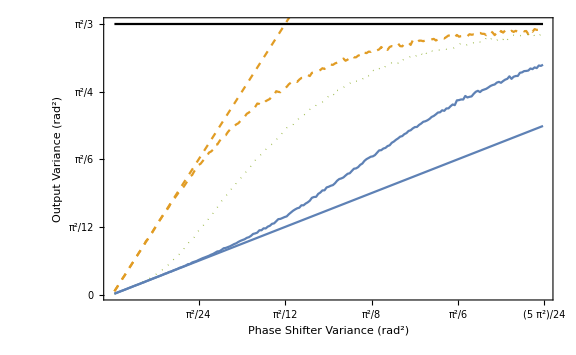

```mathematica
Show[ListPlot[{aveStepVarn4,noAveVarn4,aveEndVarn4},ImageSize->Large,FillingStyle->None,Filling->None,Joined->True,Frame->{True,True,False,False},FrameLabel->{"Phase Shifter Variance (rad^2)","Output Variance (rad^2)"},FrameTicks->{{Pi^2/24,2Pi^2/24,3Pi^2/24,4Pi^2/24,5Pi^2/24},{0,2Pi^2/24,4Pi^2/24,6Pi^2/24,8Pi^2/24}},PlotRange->{{0,5Pi^2/24},{0,Pi^2/3+0.01}},ImageSize->Small,PlotStyle->{,Directive[Dashed],Directive[Dotted,Thick]}],ListPlot[{mvnn4,mvn4,max},ImageSize->Large,FillingStyle->None,Filling->None,Joined->True,PlotStyle->{,Directive[Dashed],Black}],ImageSize->Large,BaseStyle->{FontSize->20}]
```

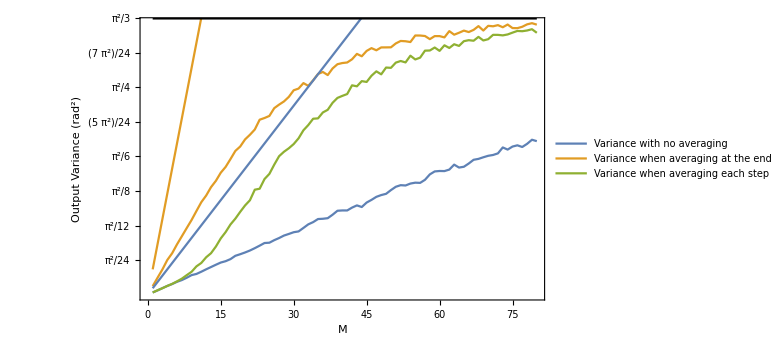

```mathematica
Show[ListPlot[{aveStepVar1,noAveVar1,aveEndVar1},PlotLegends->{"Variance with no averaging","Variance when averaging at the end","Variance when averaging each step","Predicted variance"},Joined->True,ImageSize->Large,FillingStyle->None,Frame->{True,True,False,False},FrameLabel->{"M","Output Variance (rad^2)"},FrameTicks->{Automatic,{Pi^2/24,Pi^2/12,Pi^2/8,Pi^2/6,(5 Pi^2)/24,Pi^2/4,(7 Pi^2)/24,Pi^2/3}}],Plot[{v*m/n,v*m,Pi^2/3},{m,1,mMax},PlotStyle->{,,Black}]]
```